## Contour plot for the triaxial rotor

## 2-axis quantization: ℐ_2- maximal M.O.I

### Computing the contour plot for the triaxial nucleus when the second axis has the largest moment of inertia. The parameters must correspond to positive inertial factor A and positive k number.

```mathematica
(*Expression of the Hamiltonian - classical energy function*)
```

## Constants

```mathematica
j11=11/2;
```

## Functions

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

## Energy Function

```mathematica
Hen[I_,a1_,a2_,a3_,j_,theta_,θ_,ϕ_]:=I^2(1-Sin[θ]^2)(1-ufct[I,a1,a2,a3,j,theta]*Cos[ϕ]^2-v0fct[I,a1,a2,j,theta]/I Sin[ϕ])+ufct[I,a1,a2,a3,j,theta]*I^2*Cos[ϕ]^2+2v0fct[I,a1,a2,j,theta]*I*Sin[ϕ];
contour[I_,i1_,i2_,i3_,j_,theta_]:=ContourPlot[Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,θ,ϕ],{θ,0,π},{ϕ,0,2π},PlotLegends->Automatic,Contours->13,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ_2 [rad]","φ_2 [rad]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}];
```

### First minimum point P1

```mathematica
minimum[I_,i1_,i2_,i3_,j_,theta_,left_,right_]:=Values@NMinimize[{Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,π/2,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]];
minimum[19/2,90,100,80,j11,-80,1,3]
```

1.5708

### Saddle point P2

```mathematica
saddle[I_,i1_,i2_,i3_,j_,theta_,left_,right_]:=Values@NMaximize[{Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,π/2,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]];
saddle[19/2,90,100,80,j11,-80,3,6]
```

4.07603

### Arcsin number

```mathematica
asin[I_,v_,u_]:=Print[N[ArcSin[v/(I*u)]+2π]];
asin[19/2,v0fct[19/2,IF[90],IF[100],j11,-80*π/180],ufct[19/2,IF[90],IF[100],IF[80],j11,-80*π/180]]
```

5.34875

### Draw a point on CP

```mathematica
point1[ϕ_,text_,x_,y_]:=Graphics[{Red,PointSize[0.021],Point[{π/2,ϕ}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Red,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
point2[ϕ_,text_,x_,y_]:=Graphics[{Blue,PointSize[0.021],Point[{π/2,ϕ}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Blue,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
```

### New parameters: check the positivity condition

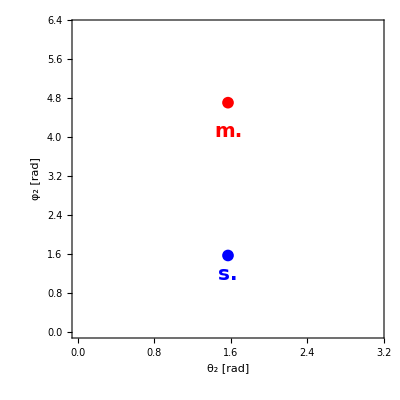

```mathematica
Show[contour[19/2,35,40,20,j13,-105],point2[1.57,"s.",0.5,0.2],point1[4.71,"m.",0.5,0.65]]
```

### Other examples

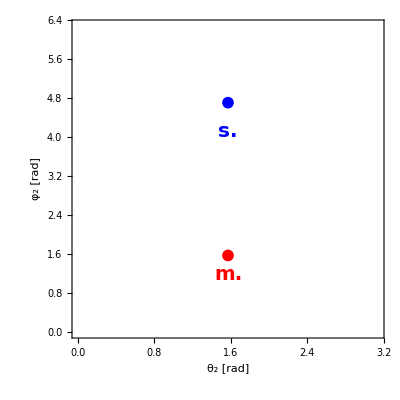

```mathematica
Show[contour[19/2,85,100,65,j13,-80],point1[1.57,"m.",0.5,0.2],point2[4.71,"s.",0.5,0.65]]
```

### Other examples: using valid params

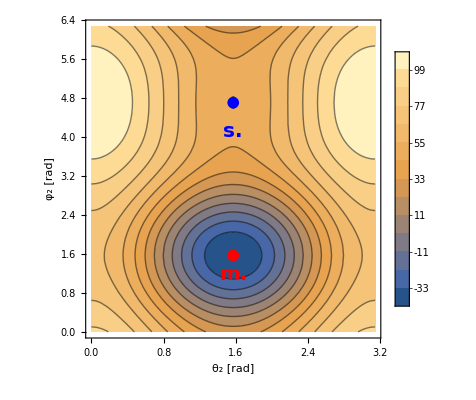

```mathematica
Show[contour[19/2,90,100,80,j11,-80],point1[1.57,"m.",0.5,0.2],point2[4.71,"s.",0.5,0.65]]
```